## Fitting procedure for solar spectra

*** Authors: Moritz Futscher, Bruno Ehrler
*** FOM institute AMOLF
*** July 2016

## Constants

```mathematica
c = 299792458.; (* units: m / s *)
h = 6.6260695729*10^-34; (* units: J s - Planck's Constant *)
T = 300.;(* units: K *)
k= 1.3807 10^-23 (*J/K*);
```

## Import AM1.5 spectra

```mathematica
AM1p5global = Drop[Import[NotebookDirectory[] <> "ASTMG173.xls"][[2, All, {1, 3}]], 2];

AM1p5direct = Drop[Import[NotebookDirectory[] <> "ASTMG173.xls"][[2, All, {1, 4}]], 2];

AM1p5diffuse = Table[{AM1p5global[[i,1]],AM1p5global[[i,2]]-AM1p5direct[[i,2]]},{i,1,Length[AM1p5global]}];
```

## Functions

```mathematica
(*Black-body radiation*)
IPlanck[T_,lambda_]:= 2 Pi h c^2 / (((lambda 10^-9)^5)( Exp[h c/((lambda 10^-9) k T)]-1))
```

```mathematica
(*Fitting procedure*)
SpectraFitPlanck[input_] := Quiet[{

spectra = input;
spectraint = Interpolation[spectra];
powerspectrum = Integrate[spectraint[wl],{wl,spectra[[1,1]],spectra[[-1,1]]}];

spectracut = Table[{i,spectraint[i]},{i,350,1050}];
spectracutint = Interpolation[spectracut];
powerspectrumcut = Integrate[spectracutint[wl],{wl,spectracut[[1,1]],spectracut[[-1,1]]}];

FitPlanck = Fit[Join[Table[{i,spectraint[i]},{i,860,890}],Table[{i,spectraint[i]},{i,1000,1040}]],{IPlanck[5777,x]},x];

difference = (1000-powerspectrumcut);
scale = spectraint[1050]-FitPlanck/.x->1050;

Addhigh = Join[
Table[{i,FitPlanck+scale/. x->i},{i,1051,1090}],
Table[{i,Fit[{{1191,FitPlanck+scale/. x->1090},{1120,FitPlanck/4+scale/. x->1140}},{1,x},x]/.x->i},{i,1191,1120}],
Table[{i,FitPlanck/4+scale/. x->1140},{i,1121,1140}],
Table[{i,Fit[{{1140,FitPlanck/4+scale/. x->1140},{1180,FitPlanck+scale/. x->1180}},{1,x},x]/.x->i},{i,1141,1180}],

Table[{i,FitPlanck+scale/. x->i},{i,1181,1310}],
Table[{i,Fit[{{1310,FitPlanck+scale/. x->1310},{1350,FitPlanck/100+scale/. x->1350}},{1,x},x]/.x->i},{i,1311,1350}],
Table[{i,FitPlanck/100+scale/4/. x->1351},{i,1351,1400}],

Table[{i,Fit[{{1400,FitPlanck/100+scale/4/. x->1420},{1515+Round[difference*0.08],FitPlanck*1.1+scale/. x->(1516+Round[difference*0.08])}},{1,x},x]/.x->i},
{i,1401,1515+Round[difference*0.08]}],
Table[{i,FitPlanck*1.1+scale/. x->i},{i,1516+Round[difference*0.08],1750}],

Table[{i,Fit[{{1750,FitPlanck*1.1+scale/. x->1750},{1810,FitPlanck/100/. x->1810}},{1,x},x]/.x->i},{i,1751,1810}],

Table[{i,FitPlanck/100/. x->1811},{i,1811,1940}],
Table[{i,Fit[{{1940,FitPlanck/100/. x->1940},{2100,FitPlanck*1+scale/. x->2100}},{1,x},x]/.x->i},{i,1941,2100}],
Table[{i,FitPlanck*1+scale/. x->i},{i,2101,2200}],
Table[{i,Fit[{{2200,FitPlanck*1+scale/. x->2200},{2525,FitPlanck/100/. x->2525}},{1,x},x]/.x->i},{i,2201,2525}],
Table[{i,0},{i,2526,2900}],
Table[{i,Fit[{{2900,FitPlanck/100/. x->2900},{3500,FitPlanck/4+scale/2/. x->3500}},{1,x},x]/.x->i},{i,2901,3500}],
Table[{i,FitPlanck/4+scale/2/. x->i},{i,3501,4000}]
];

Addlow = Join[Table[{i,0},{i,280,301}],Table[{i,Fit[{{302,0},{340,spectracut[[1,2]]}},{1,x},x]/.x->i},{i,302,340}],Table[{i,spectracut[[1,2]]},{i,341,349}]];

spectrafit = Join[Addlow,Table[{i,spectracutint[i]},{i,350,1050}],Addhigh] /.x_/;x<0->0;
spectrafitint = Interpolation[spectrafit];
powerspectrumfit = Integrate[spectrafitint[wl],{wl,spectrafit[[1,1]],spectrafit[[-1,1]]}];

}];
```

## Fit AM1.5 spectra

### AM1.5 global

```mathematica
SpectraFitPlanck[AM1p5global];
```

```mathematica
spectraglobal = spectra;
spectrafitglobal = spectrafit;
```

```mathematica
Needs["CustomTicks`"];
ticksx=LinTicks[0,4000,500,5,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
ticksy=LinTicks[0,2,0.4,1,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
```

```mathematica
Plotglobal =Show[ListLinePlot[{spectraglobal,spectrafitglobal},FrameLabel->None,PlotRange->{{200,4000},{-0.1,1.7}},AspectRatio->0.4,Frame->True,FrameTicksStyle->{{Automatic,Automatic},{{FontOpacity->0},Automatic}},FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]], PlotStyle->{{Thickness[0.005],GrayLevel[0.5]},{Thickness[0.005],ColorData[10,9]}},LabelStyle->Directive[{Bold,FontFamily->"Helvetica",FontSize->16,GrayLevel[0.1]}],FormatType->(Style[TraditionalForm[##],SingleLetterItalics->False]&),ImageSize->500,FrameTicks->{{ticksy,None},{ticksx,None}}],Epilog->Inset[Style["AM1.5 global",GrayLevel[0.1],Bold,FontFamily->"Helvetica",FontSize->18],Scaled[{0.855,0.9}]],ImagePadding->{{25,20},{20,1}}];
```

### Fitspectra AM1.5 diffuse

```mathematica
SpectraFitPlanck[AM1p5diffuse];
```

```mathematica
spectradiffuse = spectra;
spectrafitdiffuse = spectrafit;
```

```mathematica
Needs["CustomTicks`"];
ticksx=LinTicks[0,4000,500,5,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
ticksy=LinTicks[0,2,0.1,2,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
```

```mathematica
Plotdiffuse = Show[ListLinePlot[{spectradiffuse,spectrafitdiffuse},FrameLabel->None,PlotRange->{{200,4000},{-0.02,0.32}},AspectRatio->0.4,Frame->True,FrameTicksStyle->{{Automatic,Automatic},{{FontOpacity->0},Automatic}},FrameTicksStyle->{{Automatic,Automatic},{{FontOpacity->0},Automatic}},FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]], PlotStyle->{{Thickness[0.005],GrayLevel[0.5]},{Thickness[0.005],ColorData[10,9]}},LabelStyle->Directive[{Bold,FontFamily->"Helvetica",FontSize->16,GrayLevel[0.1]}],FormatType->(Style[TraditionalForm[##],SingleLetterItalics->False]&),ImageSize->500,FrameTicks->{{ticksy,None},{ticksx,None}}],Epilog->Inset[Style["AM1.5 diffuse",GrayLevel[0.1],Bold,FontFamily->"Helvetica",FontSize->18],Scaled[{0.85,0.9}]],ImagePadding->{{25,20},{20,1}}];
```

### Fitspectra AM1.5 direct

```mathematica
SpectraFitPlanck[AM1p5direct];
```

```mathematica
spectradirect = spectra;
spectrafitdirect = spectrafit;
```

```mathematica
Needs["CustomTicks`"];
ticksx=LinTicks[0,4000,500,5,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
ticksy=LinTicks[0,2,0.3,2,MajorTickLength->{.0,-0.02},MinorTickLength->{.0,-0.01}];
```

```mathematica
Plotdirect = Show[ListLinePlot[{spectradirect,spectrafitdirect},FrameLabel->None,PlotRange->{{200,4000},{-0.08,1.58}},AspectRatio->0.4,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]], PlotStyle->{{Thickness[0.005],GrayLevel[0.5]},{Thickness[0.005],ColorData[10,9]}},LabelStyle->Directive[{Bold,FontFamily->"Helvetica",FontSize->16,GrayLevel[0.1]}],FormatType->(Style[TraditionalForm[##],SingleLetterItalics->False]&),ImageSize->500,FrameTicks->{{ticksy,None},{ticksx,None}}],Epilog->Inset[Style["AM1.5 direct",GrayLevel[0.1],Bold,FontFamily->"Helvetica",FontSize->18],Scaled[{0.855,0.9}]],ImagePadding->{{25,20},{20,1}}];
```

## Plot spectra

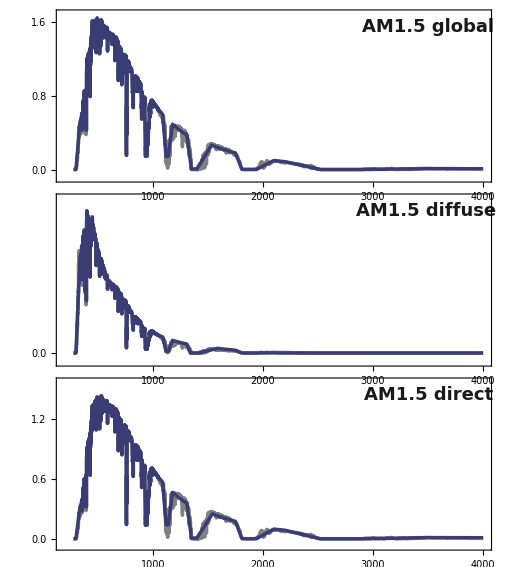
-Graphics-Spectral irradiance (W m^-2 nm^-2)Wavelength (nm)

```mathematica
Plotall = Labeled[GraphicsGrid[{{Show[Plotglobal]},{Show[Plotdiffuse]},{Show[Plotdirect]}},Frame->False,Spacings->{0,-15},AspectRatio->Full],{Rotate["Spectral irradiance (W m^-2 nm^-2)",Pi/2],"Wavelength (nm)"},{Left,Bottom},LabelStyle->Directive[{GrayLevel[0.1],Bold,FontFamily->"Helvetica",FontSize->20,SingleLetterItalics->False}]]
```